```mathematica
{d , l, X1, Y1, μ1, X2,Y2,μ2, ν,k, ϵ}= {0.8,1,3.6,0.8,0.525,0,-2.4,2.85, 1,1,0.01};
z0 = {0, 10, -0.65,10,0,0.03};
ϕ0 =  ArcSin[d/(l + z0[[6]])]
R= k ϵ^-2 δ + ν ϵ^-1 dδ
ϕ = ArcSin[d/(l + δ)]
XX = (X1 - X2)/Cos[ϕ0];
YY1 = Y1/Sin[ϕ0];YY2 = Y2/Sin[ϕ0];
σ[f_]:=Sign[f];
μμ1 = μ1 Tan[ϕ0];μμ2 = μ2 Tan[ϕ0];
subT[f_] := f/.x1->x1[t]/.x2->x2[t]/.dx1->x1'[t]/.dx2->x2'[t]/.δ->δ[t]/.σ1->Sign[x1'[t]]/.σ2->Sign[x2'[t]]/.dδ->δ'[t];
doubleδ = (Tan[ϕ]^2 dδ^2)/(l + δ) +Cos[ϕ]( Cos[ϕ0 ] XX -2Cos[ϕ] R - Cos[ϕ0]^2(σ1 Cot[ϕ0]μμ1 Abs[YY1 Sin[ϕ0] - R Sin[ϕ]] -σ2 Cot[ϕ0]μμ2 Abs[YY2 Sin[ϕ0] + R Sin[ϕ]] ) ) 
doublex1 = X1 - R Cos[ϕ] - μ1 Abs[Y1 - R Sin[ϕ]] σ1
doublex2 = X2 + R Cos[ϕ] - μ2 Abs[Y2 + R Sin[ϕ]] σ2
doubleδ = (Tan[ϕ]^2 dδ^2)/(l + δ) +Cos[ϕ]( X1 - X2 -2Cos[ϕ] R -(σ1 μ1 Abs[Y1 Sin[ϕ0] - R Sin[ϕ]] -σ2 μ2 Abs[Y2  + R Sin[ϕ]] ) )
```

0.889408

100. dδ+10000. δ

ArcSin[0.8/(1+δ)]

(0.64 dδ^2)/((1+δ)^3 (1-0.64/(1+δ)^2))+√(1-0.64/(1+δ)^2) (3.6-2 (100. dδ+10000. δ) √(1-0.64/(1+δ)^2)-0.396739 (0.525 σ1 Abs[0.8-(0.8 (100. dδ+10000. δ))/(1+δ)]-2.85 σ2 Abs[-2.4+(0.8 (100. dδ+10000. δ))/(1+δ)]))

3.6-(100. dδ+10000. δ) √(1-0.64/(1+δ)^2)-0.525 σ1 Abs[0.8-(0.8 (100. dδ+10000. δ))/(1+δ)]

(100. dδ+10000. δ) √(1-0.64/(1+δ)^2)-2.85 σ2 Abs[-2.4+(0.8 (100. dδ+10000. δ))/(1+δ)]

(0.64 dδ^2)/((1+δ)^3 (1-0.64/(1+δ)^2))+√(1-0.64/(1+δ)^2) (3.6-2 (100. dδ+10000. δ) √(1-0.64/(1+δ)^2)-0.525 σ1 Abs[0.621359-(0.8 (100. dδ+10000. δ))/(1+δ)]+2.85 σ2 Abs[-2.4+(0.8 (100. dδ+10000. δ))/(1+δ)])

```mathematica
Simplify[subT[doubleδ ]]
subT[doublex1]
subT[doublex2]
```

√(1-0.64/(1+δ[t])^2) (3.6-0.525 Abs[(0.621359-7999.38 δ[t]-80. δ'[t])/(1.+δ[t])] Sign[x1'[t]]+2.85 Abs[(2.4-7997.6 δ[t]-80. δ'[t])/(1.+δ[t])] Sign[x2'[t]]-20000. √(1-0.64/(1+δ[t])^2) (1. δ[t]+0.01 δ'[t]))+(0.64 δ'[t]^2)/((1+δ[t])^3 (1-0.64/(1+δ[t])^2))

3.6-0.525 Abs[0.8-(0.8 (10000. δ[t]+100. δ'[t]))/(1+δ[t])] Sign[x1'[t]]-√(1-0.64/(1+δ[t])^2) (10000. δ[t]+100. δ'[t])

-2.85 Abs[-2.4+(0.8 (10000. δ[t]+100. δ'[t]))/(1+δ[t])] Sign[x2'[t]]+√(1-0.64/(1+δ[t])^2) (10000. δ[t]+100. δ'[t])

```mathematica
doublex1/.σ1->1/.σ2->1
```

3.6-(0.+100. δ) √(1-0.64/(1+δ)^2)-0.525 Abs[0.8-(0.8 (0.+100. δ))/(1+δ)]

```mathematica
subT[doubleδ]
```

√(1-0.64/(1+δ[t])^2) (3.6-0.396739 (0.525 Abs[0.8-(0.8 (0.+100. δ[t]))/(1+δ[t])]-2.85 Abs[-2.4+(0.8 (0.+100. δ[t]))/(1+δ[t])])-2 (0.+100. δ[t]) √(1-0.64/(1+δ[t])^2))+(0.64 δ'[t]^2)/((1+δ[t])^3 (1-0.64/(1+δ[t])^2))

```mathematica
ysol1=NDSolveValue[{δ''[t]==subT[doubleδ],δ'[0]== z0[[5]], δ[0]== z0[[6]]}, δ,{t,0,5}]
```

NDSolveValue::underdet: There are more dependent variables, {x1[t],x2[t],δ[t]}, than equations, so the system is underdetermined.

NDSolveValue[{δ''[t]==√(1-0.64/(1+δ[t])^2) (3.6-0.396739 (0.525 Abs[0.8-(0.8 (0.+100. δ[t]))/(1+δ[t])] Sing[x1'[t]]-2.85 Abs[-2.4+(0.8 (0.+100. δ[t]))/(1+δ[t])] Sing[x2'[t]])-2 (0.+100. δ[t]) √(1-0.64/(1+δ[t])^2))+(0.64 δ'[t]^2)/((1+δ[t])^3 (1-0.64/(1+δ[t])^2)),δ'[0]==0,δ[0]==0.03},δ,{t,0,5}]

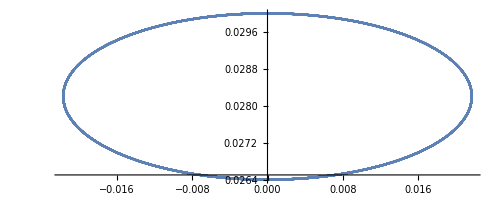

```mathematica
ParametricPlot[{ysol1'[t], ysol1[t]},{t,0,5},PlotRange->Full]
```

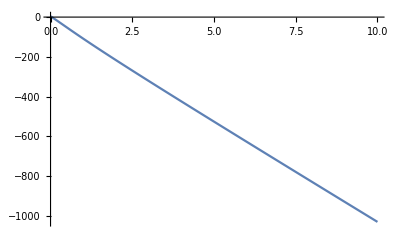

```mathematica
Plot[doublex1/.σ1->1/.σ2->1, {δ,0,10}]
```

```mathematica
ysol=NDSolveValue[{x1''[t] == subT[doublex1],x2''[t] == subT[doublex2],δ''[t]==subT[doubleδ], x1[0]==z0[[1]],x1'[0]==z0[[2]],x2[0]==z0[[3]],x2'[0]==z0[[4]],δ'[0]== z0[[5]], δ[0]== z0[[6]]},{x1,x2, δ},{t,0,4}]
```

{InterpolatingFunction[{{0., 4.}}, <>],InterpolatingFunction[{{0., 4.}}, <>],InterpolatingFunction[{{0., 4.}}, <>]}

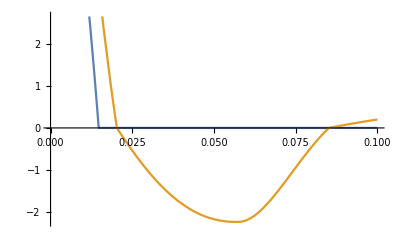

```mathematica
Plot[{ysol[[2]]'[t],ysol[[1]]'[t]},{t,0,0.1}]
```

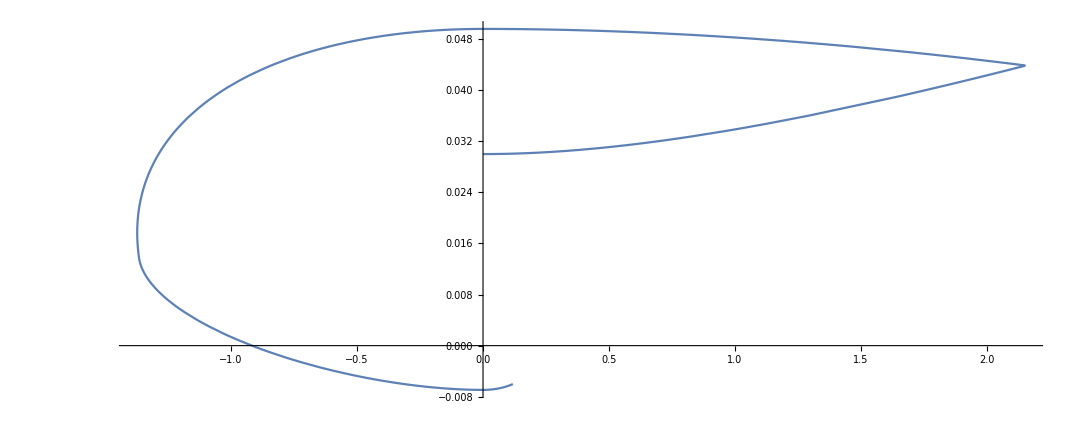

```mathematica
ParametricPlot[{ysol[[3]]'[t], ysol[[3]][t]},{t,0,0.1},PlotRange->Full]
```

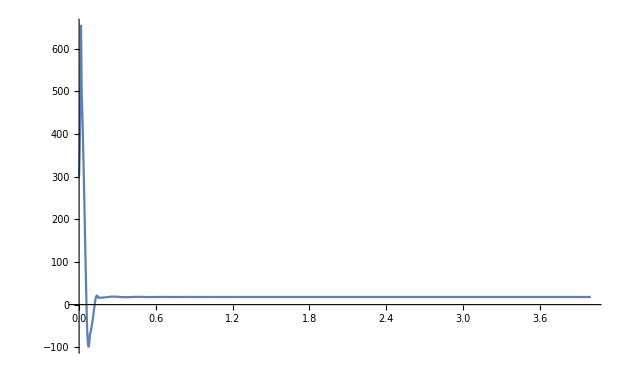

```mathematica
Plot[ysol[[3]][t] k ϵ^-2 +ν ϵ^-1 ysol[[3]]'[t],{t,0,4},PlotRange->Full]
```

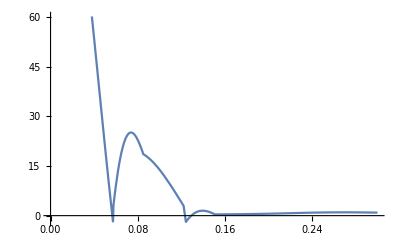

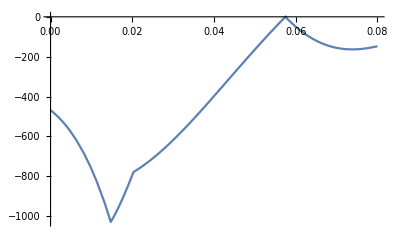

```mathematica
Plot[Abs[X1 -Cos[ϕ0]( ysol[[3]][t] k ϵ^-2+ν ϵ^-1 ysol[[3]]'[t])]- μ1 Abs[Y1 - Sin[ϕ0](ysol[[3]][t] k ϵ^-2+ν ϵ^-1 ysol[[3]]'[t])],{t,0,0.3}]
Plot[Abs[X2 +Cos[ϕ0]( ysol[[3]][t] k ϵ^-2+ν ϵ^-1 ysol[[3]]'[t])]- μ2 Abs[Y2 + Sin[ϕ0](ysol[[3]][t] k ϵ^-2+ν ϵ^-1 ysol[[3]]'[t])],{t,0,0.08}]
```

```mathematica
σ[f_]:=Sign[f]
ysol=NDSolveValue[{δ''[t]==σ[δ'[t]]-2 δ[t]^2,δ[0]== -1, δ'[0]== -1},δ,{t,0,2}]
```

NDSolveValue::ndsz: At t == 1.69385, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[{{0., 1.69385}}, <>]